# Výkony

## Jak počítat výkon - úvod

```mathematica
(* Výkon/Příkon značíme P *)
P = u*i
P = u^2/R
P = i^2*R

(* Co je to efektivní hodnota napětí *)
(* Efektivní hodnota střídavého napětí (Uef) je rovna hodnotě stejnosměrného napětí, které by při přiložení na odporovou zátěž dávalo stejný průměrný výkon.*)
(* Jak vypočítat efektivní hodnotu *)
Ueff = amplituda/(√2)
amplituda = Ueff*√2
```

## Příklady

```mathematica
(* PŘÍKLAD 19 *)
(* Elektrická zásuvka ve zdi je dimenzována na maximální proud 10 A.Jaký maximální příkon může mít spotřebič,který do této zásuvky můžeme připojit?Napětí v zásuvce je 230 V. *)
```

```mathematica
ClearAll["Global`*"]
Iz = 10;
Uef = 230;
P = Uef*Iz
```

2300

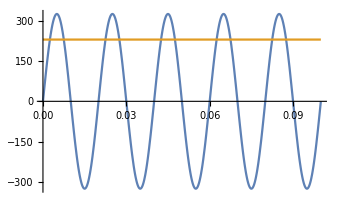

```mathematica
-Graphics-;
(* Efektivní hodnota střídavého napětí (Uef) je rovna hodnotě stejnosměrného napětí, které by při přiložení na odporovou zátěž dávalo stejný průměrný výkon.*)
ClearAll["Global`*"]
frekvence = 50;
perioda = 1/frekvence;
tmax = 5*perioda;
Uef = 230;
amplituda = Uef*√2;
zasuvka = amplituda*Sin[2*π*frekvence*t];
Plot[{zasuvka, Uef},{t,0,tmax}]
```

```mathematica
(* PŘÍKLAD 20 *)
(* Můžeme do elektrické zásuvky s maximálním povoleným proudem 16 A připojit elektrickou troubu,která v turbo režimu má příkon 3,6 kW? Napětí v zásuvce je 230 V. *)

ClearAll["Global`*"]
Izmax = 16;
Uef = 230;
Ptrouba = 3.6*10^3;

Pz = Uef*Izmax
Pz>Ptrouba
```

3680

True

```mathematica
(* PŘÍKLAD 21 *)
(*Rychlovarná konvice není nic jiného nežli výkonový rezistor.Konvice má na svém štítku údaj o tom,že při napětí Ueff=220 V má tepelný výkon 1850 W.
Jak velký je proud,který teče konvicí?
Jaký odpor má konvice?Jak se změní výkon konvice,pokud se napětí v zásuvce zvýší na Ueff=240 V?
Na jakou hodnotu přitom vzroste proud,který teče konvicí (na alespoň takovýto proud musí být zásuvka dimenzována).
*)
```

```mathematica
ClearAll["Global`*"]
UefCR = 220.;
Pkonvice = 1850;
Ikonvice = Pkonvice/UefCR
Rkonvice = UefCR/Ikonvice
UefF = 240.;
(* P = U*I == U^2/R== U*U/R *)
PkonviceF =UefF^2/Rkonvice
IkonviceF = PkonviceF/UefF
```

8.40909

26.1622

2201.65

9.17355

```mathematica
(* PŘÍKLAD 22 *)
(* 
Také elektrická plotýnka sporáku není nic jiného nežli výkonový rezistor. Plotýnka má jmenovitý výkon 600 W (jmenovitý výkon je výkon při jmenovitém napětí v elektrické síti,což je v našich končinách 230 V).
Jak velký odpor má plotýnka?
Jak velký proud teče plotýnkou při jmenovitém napětí?
Napětí v síti může kolísat mezi 220 V a 240 V. Určete,jak může kolísat výkon plotýnky. Určete,jak může kolísat proud plotýnkou. V jakém rozmezí bude kolísat amplituda napětí?
*)
```

```mathematica
ClearAll["Global`*"]
Pplotynka = 600.;
Uef = 230.;


Rplotynka = Uef^2/Pplotynka
Iplotynka = Pplotynka/Uef
Rplotynka1 = Uef/Iplotynka

Ukolisani ={220.,240.}
Pkolisani = Ukolisani^2/Rplotynka
Iplotynka = Pplotynka/Ukolisani

amplituda = √2*Ukolisani
```

88.1667

2.6087

88.1667

{220.,240.}

{548.96,653.308}

{2.72727,2.5}

{311.127,339.411}

```mathematica
(* PŘÍKLAD 23 *)
(*
Elektrická trouba má příkon až 3,5 kW.Na jaký proud musejí být dimenzovány přívodní vodiče,jestliže je trouba napájena z napětí 230 V?
*)
```

```mathematica
ClearAll["Global`*"]
Ptrouba = 3.5*10^3;
Ueff = 230;
Imax = Ptrouba/Ueff
```

15.2174